```mathematica
segmentImage[binarizedMask_?ImageQ,opt:"ConnectedComponents"|"Watershed":"Watershed",
threshCellsize_:20000]:= Module[{seg,areas,
indexMaxarea,maxArea,indsmallareas={},$ind},
seg= Switch[opt,"ConnectedComponents",
(* assuming we input 0 as foreground and 1 as background. ConnectedComponents is a more general segmentation framework *)
MorphologicalComponents[ColorNegate@binarizedMask, CornerNeighbors->False],
"Watershed",
(* for epithelial cells *)
WatershedComponents[binarizedMask, CornerNeighbors->False]
];
areas=ComponentMeasurements[seg,"Area"];
{indexMaxarea,maxArea}=First@MaximalBy[areas,Last]/.Rule-> List;
indsmallareas = Keys@Cases[areas,HoldPattern[_-> 1.]];
If[maxArea >= threshCellsize||indsmallareas!= {},
$ind={indexMaxarea}~Join~indsmallareas;
seg=ArrayComponents[seg,Length@areas,Thread[$ind->0]]
];
seg
];
```

```mathematica
ClearAll[associateVertices];
Options[associateVertices]= {"stringentCheck"-> True};
associateVertices[img_,segt_,maskDil_:2,OptionsPattern[]]:= With[{dim =Reverse@ImageDimensions@img,
stringentQ=OptionValue["stringentCheck"]},
Module[{pts,members,vertices,nearest,vertexset,likelymergers,imagegraph,imggraphweight,imggraphpts,vertexpairs,
posVertexMergers,meanVertices,Fn},

pts = ImageValuePositions[MorphologicalTransform[img,{"Fill","SkeletonBranchPoints"}], 1]; (* finding branch points *)
members = ParallelMap[Block[{elems},
 elems = Dilation[ReplaceImageValue[ConstantImage[0,Reverse@dim],#->1],1];
 DeleteCases[Union@Flatten@ImageData[elems*Image[segt]],0.]
 ]&,pts]; 
 
vertices = Cases[Thread[Round@members-> pts],HoldPattern[pattern:{__}/;Length@pattern >= 2 -> _]];
(* finding vertices with 2 or more neighbouring cells *)

nearest = Nearest[Reverse[vertices, 2]]; (* nearest func for candidate vertices *)
Fn = GroupBy[MapAt[Sort,(#-> nearest[#,{All,3}]&/@Values[vertices]),{All,2}],Last->First,#]&;

Which[Not@stringentQ,
 (* merge if candidate vertices are 2 manhattan blocks away. Not a stringent check for merging *)
 KeyMap[Union@*Flatten]@Fn[List@*N@*Mean]//Normal,
 stringentQ,
 (* a better check is to see the pixels separating the vertices are less than 3 blocks *)
 vertexset = Fn[Identity];
 (* candidates for merging*)
 likelymergers = Cases[Normal[vertexset],PatternSequence[{{__Integer}..}-> i:{__List}/;Length[i]>= 2]];
 (*defining graph properties of the image *)
 imagegraph = MorphologicalGraph@MorphologicalTransform[img,{"Fill"}];
 imggraphweight = AssociationThread[(EdgeList[imagegraph]/.UndirectedEdge->List )-> PropertyValue[imagegraph,EdgeWeight]];
 imggraphpts = Nearest@Reverse[Thread[VertexList[imagegraph]-> PropertyValue[imagegraph,VertexCoordinates]],2];
 (* corresponding nodes on the graph *)
 vertexpairs = Union@*Flatten@*imggraphpts/@(Values[likelymergers]);
 (* find pairs < than 3 edgeweights away, take a mean of vertices and update the association with mean position *)
 posVertexMergers = Position[Thread[Lookup[imggraphweight,vertexpairs]< 3],True];
 If[posVertexMergers != {},
  meanVertices=MapAt[List@*N@*Mean,likelymergers,Thread[{Flatten@posVertexMergers,2}]];
  Scan[(vertexset[#[[1]]]=#[[2]])&,meanVertices]
  ];
  KeyMap[Union@*Flatten]@vertexset//Normal]
  ]
];
```

```mathematica
ForceInference[filename_]:=Module[{Img,segmentation,maxcellLabels,cellsToVertices,vertexnum,edges,smalledges,maxedgeLabels,edgeEndPoints,nearest,nearestedgeEndPoints,edge2pixLabels,pos,oldCoords,vertexAssoc,vertexToCells,filteredvertices,filteredvertexnum,relabelvert,edgeLabels,edgenum,spArrayTx,spArrayTy,vertexCoordinatelookup,vertexpairs,vertexvertexConn,inds,edgelabelToVert,vertToedges,cols,colsOrder,edgeImg,tensinds,tx,ty,spArrayPx,pt,spArrayPy,spArrayX,spArrayY,pvals,pressurecolours,ptsEdges,ord,k,v,edgeptAssoc,poly,pts,mean,sol,spA,spB,spb,spg,SMatrix,h,Q,R,H,n,m,p,logL,μ,τ,tvals,orderpts,ordering,cellToVertexLabels,delV,cellToAllVertices,removecollabels,members,nlab,collabels,
range=10.0^Range[-1.5,1.5,0.1]},
LaunchKernels[];
Img= ColorConvert[Import[filename],"Grayscale"];
Print[Image[Img,ImageSize->Medium]];
segmentation= segmentImage[Img];
Print["Image segmented: ", Style["☑",20]];
maxcellLabels = Max@Values@ComponentMeasurements[segmentation,"LabelCount"];
cellsToVertices=associateVertices[Binarize@Img,segmentation];
Print["vertices found and associated: ", Style["☑",20]];
vertexnum=Length@cellsToVertices;
edges=MorphologicalComponents@ImageFilter[If[#[[3,3]] == 1 && Total[#[[2;;-2,2;;-2]],2] == 3, 1, 0]&,Img,2];
(* associate vertices with all edges. for pixel value 1 edge find two nearest pts. 
for all edges <3, merge the pts together; make changes to the cellToVertex *)
(* edges to be deleted *)
smalledges=Flatten[Position[Values@ComponentMeasurements[edges,"Count"],1|2]];
maxedgeLabels=Max@edges;
edgeEndPoints=With[{comp=Values@ComponentMeasurements[edges,"Mask"]},
ParallelTable[
If[Total[#] == 1,
ImageValuePositions[#,1],
ImageValuePositions[MorphologicalTransform[#,"SkeletonEndPoints"],1]]&@Binarize@Image[comp[[i]]]
,{i,maxedgeLabels}]
];
(* for small edge: if one pixel just delete *)
edges=Fold[If[Length@edgeEndPoints[[#2]]==1,#1/.#2 -> 0,#1]&,edges,smalledges];
nearest=Nearest@Flatten[Values[cellsToVertices],1];
nearestedgeEndPoints=Map[Flatten@*nearest,edgeEndPoints,{2}];
(* if edge is two pixels then put average value in the cellsToVertices: *)
edge2pixLabels=Keys@Cases[ComponentMeasurements[edges,"Count"],HoldPattern[_-> 2]];

If[edge2pixLabels≠{},
(oldCoords=nearestedgeEndPoints[[#]];
pos=Position[cellsToVertices,#,Infinity]&/@oldCoords;
cellsToVertices=Fold[ReplacePart[#1,#2-> Mean@oldCoords]&,cellsToVertices,pos]
)&/@edge2pixLabels
];
edges=ArrayComponents[edges/.Thread[edge2pixLabels-> 0]];
Print["edges found and associated: ", Style["☑",20]];
cellsToVertices=Normal@AssociationMap[Reverse,GroupBy[cellsToVertices,Last-> First,Union@*Flatten]];
vertexnum=Length@cellsToVertices;
nearest=Nearest@Flatten[Values@cellsToVertices,1];
edgeEndPoints=Delete[edgeEndPoints,Partition[smalledges,1]];
nearestedgeEndPoints=Map[Flatten@*nearest,edgeEndPoints,{2}];
vertexAssoc= AssociationThread[Flatten[Values@cellsToVertices,1],Range@vertexnum];
vertexToCells=Reverse[MapAt[vertexAssoc[#]&,MapAt[Flatten,cellsToVertices,{All,2}],{All,2}],2];
(* Tension*)
filteredvertices=Keys@Select[<|vertexToCells|>,(Length[#]>2&)];
filteredvertexnum=Length@filteredvertices;
(* till above we have isolated all vertices that share three edges; we can relabel those filtered vertices to be the rows of the matrix *)
relabelvert=AssociationThread[filteredvertices-> Range[Length@filteredvertices]];
(* all edges are relabeled to have a unique identity *)
edgeLabels=AssociationThread[Range[Length@#]->#]&[nearestedgeEndPoints];
edgenum=Max[Keys@edgeLabels];
vertexCoordinatelookup=AssociationMap[Reverse,vertexAssoc];(* given the vertex label -> get the coordinates from the original lookup *)
vertexpairs=Map[vertexAssoc,nearestedgeEndPoints,{2}];
(* edge coordinates to vertex label. take vertices one by one and find all the edges it is a part of. None should be less than 3 *)
vertexvertexConn= ParallelTable[
Cases[vertexpairs,{OrderlessPatternSequence[i,p_]}:> {i,p}],
{i,filteredvertices}];
delV=Cases[vertexvertexConn,{{p_,_},{p_,_}}:> p];
vertexvertexConn=DeleteCases[vertexvertexConn,{_,_}];
inds=Flatten[vertexvertexConn,1];
(* edgelabel -> vertices *)
edgelabelToVert=Map[vertexAssoc,edgeLabels,{2}];
(*vertices -> edgelabel *)
vertToedges=Normal@AssociationMap[Reverse,edgelabelToVert];
colsOrder=Flatten[Cases[vertToedges,PatternSequence[{OrderlessPatternSequence@@#}-> p_]:> p,Infinity]&/@inds];
edgeImg=Graphics[{Thickness[0.005],Line@Lookup[vertexCoordinatelookup,edgelabelToVert[#]]&/@colsOrder}];
{tx,ty}=Transpose[
With[{target=vertexCoordinatelookup[#[[2]]],source=vertexCoordinatelookup[#[[1]]]},
(target-source)/Norm[target-source]
]&/@inds];

filteredvertices=Complement[filteredvertices,delV];
Print["checking robustness for vertex association (force balance done on Blue):"];
Print[Show[Img,Graphics[{Yellow,PointSize[0.015],Point@Complement[Flatten[nearestedgeEndPoints,1],#],Blue,Point@#}&@Lookup[vertexCoordinatelookup,filteredvertices]]]];
Print["checking robustness for tension coefficients:"];
Print[SortBy[Length[#]->Framed@Graphics[{RandomColor[],Thickness[0.1],Line@#},ImageSize->25]&/@Map[vertexCoordinatelookup,vertexvertexConn,{3}],
First]];

Print["Tension coefficients computed: ",Style["☑",20]];
MapThread[Print[Style["counts of zero coefficients "<>#1,Red], Count[#2,0.]]&,{{"Tx: ","Ty: "},{tx,ty}}];

filteredvertexnum=Length@filteredvertices;
relabelvert=AssociationThread[filteredvertices-> Range[Length@filteredvertices]];

tensinds=Thread[{Lookup[relabelvert,Part[inds,All,1]],colsOrder}];
spArrayTx=spArrayTy=SparseArray@ConstantArray[0,{filteredvertexnum,edgenum}];

MapThread[(spArrayTx[[Sequence@@#1]]=#2)&,{tensinds,tx}];
MapThread[(spArrayTy[[Sequence@@#1]]=#2)&,{tensinds,ty}];
spArrayPx=spArrayPy=SparseArray@ConstantArray[0,{filteredvertexnum,maxcellLabels}];

MapThread[Print[Style[#1<> "coefficients stats: ",Blue],Counts@Map[Total@*Unitize,Normal[#2]]]&,
{{"Tx ", "Ty "},{spArrayTx,spArrayTy}}];
Print[Style["Tension coefficients dist: ",Bold],Histogram[{{},Join[spArrayTx["NonzeroValues"],spArrayTy["NonzeroValues"]]},20,
ImageSize->Small]];

Block[{neighbouringCells,bisectionlabels,bisectpts,centroid,orderingT,px,py,
vertexcoords,orderptsT,orderIndT,orderCells,kk=0},
With[{cellToVertexLabelsT= Reverse[vertexToCells,2],
edgeVertexPart=GroupBy[vertexvertexConn~Flatten~1 ,First-> Last]},
With[{cellToAllVerticesT= GroupBy[Flatten[Thread/@cellToVertexLabelsT],First-> Last]},
Do[
neighbouringCells= vertexToCells[[i,2]]; (* for vertex, the neighbouring cell labels *)
bisectionlabels=Intersection[cellToAllVerticesT[#],edgeVertexPart[i]]&/@neighbouringCells ;
If[Length[neighbouringCells]>2 && MatchQ[bisectionlabels,{Repeated[{_,_},{3,∞}]}],
(*Print[i," : ",neighbouringCells];*)
(vertexcoords=DeleteDuplicates[vertexCoordinatelookup[#]&/@Flatten@bisectionlabels];
centroid=Mean@vertexcoords;
orderingT=Ordering[ArcTan[Last@#-Last@centroid,First@#-First@centroid]&/@vertexcoords];
orderptsT=vertexcoords[[orderingT]];
orderIndT=Partition[Lookup[vertexAssoc,Append[orderptsT,First@orderptsT]],2,1];
 orderCells =
Last@@@Position[(x↦ Map[Intersection[x,#]&,orderIndT])/@(cellToAllVerticesT[#]&/@neighbouringCells),x_/;Length[x]==2];
neighbouringCells=neighbouringCells[[orderCells]];
bisectpts=Map[vertexCoordinatelookup,orderIndT,{2}];
{px,py}=Transpose[{(#[[2,2]]-#[[1,2]])/2,-(#[[2,1]]-#[[1,1]])/2}&/@bisectpts];
If[MemberQ[px,0.]||MemberQ[py,0.],kk++];
{px,py})
];
Scan[(spArrayPx[[ Sequence@@#[[1]] ]]=#[[2]])&,Thread[Thread[{relabelvert@i,neighbouringCells}]-> px]];
Scan[(spArrayPy[[ Sequence@@#[[1]] ]]=#[[2]])&,Thread[Thread[{relabelvert@i,neighbouringCells}]-> py]],
{i,filteredvertices}]
]
];
Print["Pressure coefficients computed: ",Style["☑",20]];
Print[Style["Pressure coefficients zero: ",Red],kk ];
];

MapThread[Print[Style[#1<> "coefficients stats: ",Blue],Counts@Map[Total@*Unitize,Normal[#2]]]&,
{{"Px ", "Py "},{spArrayPx,spArrayPy}}];
Print[Style["pressure coefficients dist: ",Bold],
Histogram[{{},Join[spArrayPx["NonzeroValues"],spArrayPy["NonzeroValues"]]},ImageSize->Small]];
spArrayX=Join[spArrayTx,spArrayPx,2];
spArrayY=Join[spArrayTy,spArrayPy,2];

cellToVertexLabels= Reverse[vertexToCells,2];
cellToAllVertices= GroupBy[Flatten[Thread/@cellToVertexLabels],First-> Last];

(* polygons *)
ptsEdges ={{1,1},Reverse@Dimensions[segmentation],{Last[Dimensions@segmentation],1},{1,First[Dimensions@segmentation]}};
{k,v}={Keys@#,Values[#][[All,2]]}&@ComponentMeasurements[segmentation,{"AdjacentBorderCount","Centroid"},#==2&];
ord=Flatten[Function[x,Position[#,Min[#]]&@Map[EuclideanDistance[#,x]&,ptsEdges]]/@v];
edgeptAssoc=Association[Rule@@@Thread[{k,ptsEdges[[ord]]}]];
poly=(
pts=vertexCoordinatelookup/@cellToAllVertices[#];
If[MemberQ[k,#],AppendTo[pts,edgeptAssoc[#]],pts];
mean=Mean[pts];
ordering=Ordering[ArcTan[Last@#-Last@mean,First@#-First@mean]&/@pts];
orderpts=pts[[ordering]];
Polygon@Append[orderpts,First@orderpts]
)&/@Range[maxcellLabels];

Print["checking robustness for pressure coefficients:"];
Print@With[{map=Map[vertexCoordinatelookup,vertexvertexConn,{3}]},
Table[
pt=vertexCoordinatelookup[i];(*check*)
members=Lookup[vertexToCells,i];
nlab=relabelvert[i];
pts=Part[Flatten[map[[nlab]],1],2;;All;;2];
mean=Mean@pts;
ordering=Ordering[ArcTan[Last@#-Last@mean,First@#-First@mean]&/@pts];
orderpts=pts[[ordering]];
Framed@Graphics[{{Thread[{Table[ColorData["Rainbow"][0.19*i],{i,Length@members}],poly[[members]]}]},{PointSize[0.05],Black,Point@pt},{Thread[{{Red,Darker@Green,Blue},PointSize[0.05],Point/@orderpts}]},{Purple,Thick,Dashed,Arrowheads[.1],Arrow[Append[orderpts,First@orderpts]]}},
ImageSize->Tiny],{i,filteredvertices}]
];

Print[Style["\nwith maximum likelihood",Bold,18]];
(* maximizing Log-likelihood function *)
sol=With[{ls=range},
(*spA=SparseArray@(Join[spArrayX,spArrayY]);*)
spA=SparseArray@(Flatten[Transpose[{spArrayX,spArrayY}],1]);
spg=SparseArray@(ConstantArray[1.,Last[Dimensions@spArrayTx]]~Join~ConstantArray[0.,Last[Dimensions@spArrayPx]]);
spB=SparseArray@DiagonalMatrix[spg];
n=First@Dimensions@spA;
m=(Length[#]-Total@#)&@Diagonal[spBᵀ.spB];
With[{DimspB=First[Dimensions@spB]},
spb=SparseArray@ConstantArray[0.,First[Dimensions@spA]];
Table[
(τ=Sqrt[μ];
SMatrix=SparseArray@(Map[Flatten]@Transpose[{Join[spA,τ spB],Join[spb,τ spg]},{2,1}]);
{Q,R}=SparseArray/@QRDecomposition[SMatrix];
R=DiagonalMatrix[Sign[Diagonal@R]].R;
H=R[[;;#,;;#]]&@DimspB;
h⃗=R[[;;#,#+1]]&@DimspB;
h=R[[#+1,#+1]]&@DimspB;
logL=-(n-m+1)*Log[h^2]+Total[Log[Diagonal[μ (spBᵀ.spB)]["NonzeroValues"]]]-2*Total[Log[Diagonal[H[[1;;-2,1;;-2]]]["NonzeroValues"]]]
),{μ,ls}]
]
];

Print[ListPlot[{sol,sol},Joined-> {True,False},PlotStyle->{{Red,Thick},{PointSize[0.02],Black}},AxesStyle->{{Black},{Black}},AxesLabel->{"index μ","LogLikelihood"},Background->LightBlue]];
μ=Keys@@MaximalBy[Thread[range-> sol],Values,1];
Print["optimized value of μ: ",μ];
τ=Sqrt[μ];
With[{DimspB=First[Dimensions@spB]},
SMatrix=SparseArray@(Map[Flatten]@Transpose[{Join[spA,τ spB],Join[spb,τ spg]},{2,1}]);
{Q,R}=SparseArray/@QRDecomposition[SMatrix];
R=DiagonalMatrix[Sign[Diagonal@R]].R;
H=R[[;;#,;;#]]&@DimspB;
h⃗=R[[;;#,#+1]]&@DimspB;
];
p =PseudoInverse[H].h⃗;
tvals=Rescale@p[[ 1;;Last[Dimensions@spArrayTx] ]];
cols=ColorData["Rainbow"][#]&/@tvals; 
Print["Tension map:"];
Print[Graphics[{Thickness[0.005],Riffle[cols,Line/@Values@edgeLabels]}]];
pvals=p[[ Last[Dimensions@spArrayTx]+1;;]];
removecollabels=Keys@ComponentMeasurements[segmentation,"AdjacentBorders",Length[#]>0&];
collabels=Complement[Range@maxcellLabels,removecollabels];
pressurecolours=ColorData["Rainbow"][#]&/@Rescale[(pvals[[collabels]])];
Print["Pressure map:"];
Print@Show[Graphics@Riffle[pressurecolours,poly[[collabels]]],edgeImg]; 
];
```

-Graphics-

Image segmented: ☑

vertices found and associated: ☑

edges found and associated: ☑

checking robustness for vertex association (force balance done on Blue):

-Graphics-

checking robustness for tension coefficients:

{3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,3→-Graphics-,4→-Graphics-,4→-Graphics-,4→-Graphics-}

Tension coefficients computed: ☑

counts of zero coefficients Tx: 16

counts of zero coefficients Ty: 9

Tx coefficients stats: <|3→376,2→16,4→3|>

Ty coefficients stats: <|3→383,2→9,4→3|>

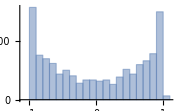
Tension coefficients dist: -Graphics-

Pressure coefficients computed: ☑

Pressure coefficients zero: 15

Px coefficients stats: <|3→387,2→5,4→3|>

Py coefficients stats: <|3→382,4→3,2→10|>

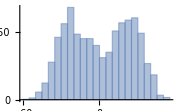
pressure coefficients dist: -Graphics-

checking robustness for pressure coefficients:

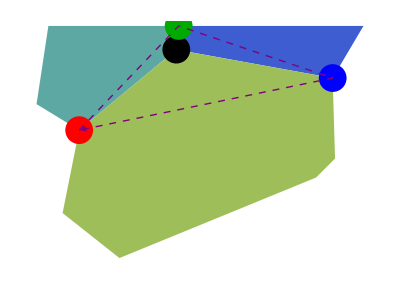
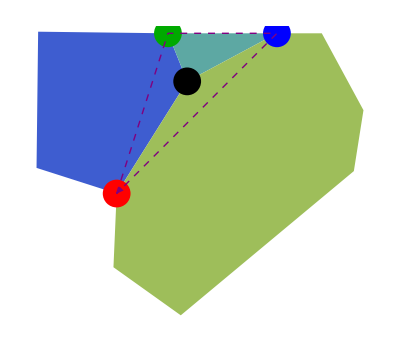
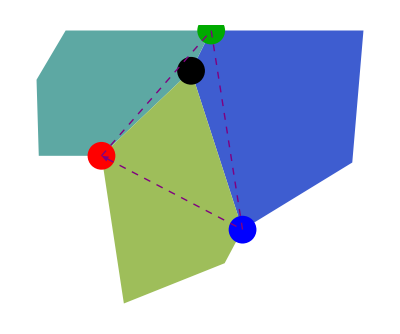
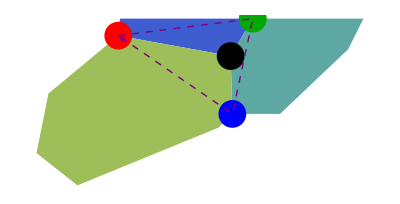
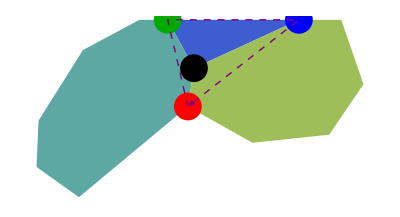
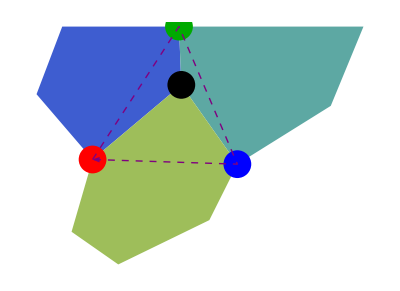
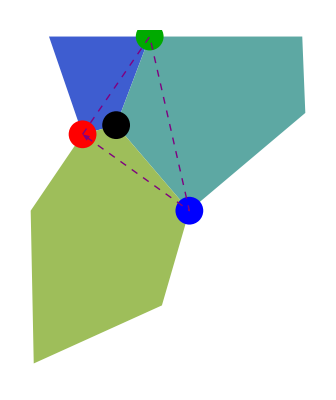
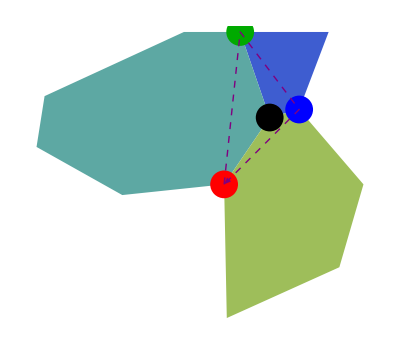
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

with maximum likelihood

-Graphics-

optimized value of μ: 0.630957

Tension map:

-Graphics-

Pressure map:

-Graphics-

{65.0746,Null}

```mathematica
Quiet[AbsoluteTiming@ForceInference["C:\\Users\\aliha\\Desktop\\wolfram force inference\\image.tif"]]
```